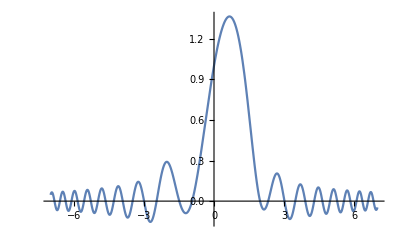

```mathematica
sol:=DSolve[y'[x]+x*y[x]==Cos[x^2],y,x]
Plot[Evaluate[y[x]/.sol/.{C[1]->1}],{x,-7,7},PlotRange->All]
```